```mathematica
m1={{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,0}}
```

{{0,1,0,0},{0,0,1,0},{0,0,0,1},{1,0,0,0}}

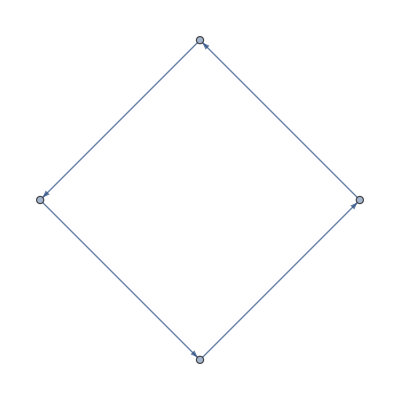

```mathematica
AdjacencyGraph[m1]
```

```mathematica
Det[m1]
```

-1

```mathematica
Tr[m1]
```

0

```mathematica
ei1=Eigenvalues[m1]
```

{-1,ⅈ,-ⅈ,1}

```mathematica
p[x_]=CharacteristicPolynomial[m1,x]
```

-1+x^4

```mathematica
r1[i_]:=x/.NSolve[p[x]==0,x][[i]]
```

```mathematica
et1=Sum[Abs[r1[i]],{i,4}]
```

4.

```mathematica
(*elliptical tristate as a Weeks minimal volume hyperbolic manifold <r,r,l>or<l,l,r>*)
```

```mathematica
m2={{0,1,0},{0,0,1},{1,1,0}}
```

{{0,1,0},{0,0,1},{1,1,0}}

```mathematica
AdjacencyGraph[m2]
```

-Graphics-

```mathematica
(*Isospectral*)
```

```mathematica
Eigenvalues[Transpose[m2]]
```

{Root1.32Root[-1-#1+#1^3&,1]1.324717957244746,Root-0.662+0.562 ⅈRoot[-1-#1+#1^3&,3]-0.662358978622373,Root-0.662-0.562 ⅈRoot[-1-#1+#1^3&,2]-0.662358978622373}

```mathematica
AdjacencyGraph[Transpose[m2]]
```

-Graphics-

```mathematica
Det[m2]
```

1

```mathematica
Tr[m2]
```

0

```mathematica
ei2=Eigenvalues[m2]
```

{Root1.32Root[-1-#1+#1^3&,1]1.324717957244746,Root-0.662+0.562 ⅈRoot[-1-#1+#1^3&,3]-0.662358978622373,Root-0.662-0.562 ⅈRoot[-1-#1+#1^3&,2]-0.662358978622373}

```mathematica
q[x_]=CharacteristicPolynomial[m2,x]
```

1+x-x^3

```mathematica
r2[i_]:=x/.NSolve[q[x]==0,x][[i]]
```

```mathematica
(*Particle two tristate has energy 3.062391880910165*me*c^2*)
```

```mathematica
et2=Sum[Abs[r2[i]],{i,3}]
```

3.06239

```mathematica
(* 2*e(up)+2*e(down)+photon-> Tristate+e(up) or e[down)*)
```

```mathematica
et1-et2-1
```

-0.0623919

```mathematica
(* 13 particle 1 (D_6)goes to 16 particle2 +photon energy 0.0017299054373580702*me*c^2*)
```

```mathematica
4*(3et1-4et2)+1
```

0.00172991

```mathematica
((r2[3]*et2/et1-1)*137.03608-2)*137.03698+74/10
```

0.0138897

```mathematica
m3={{0,1,0,0},{0,0,1,0},{1,1,0,0},{0,0,0,1}}
```

{{0,1,0,0},{0,0,1,0},{1,1,0,0},{0,0,0,1}}

```mathematica
AdjacencyGraph[m3]
```

-Graphics-

```mathematica
Det[m3]
```

1

```mathematica
Tr[m3]
```

1

```mathematica
ei3=Eigenvalues[m3]
```

{Root1.32Root[-1-#1+#1^3&,1]1.324717957244746,1,Root-0.662+0.562 ⅈRoot[-1-#1+#1^3&,3]-0.662358978622373,Root-0.662-0.562 ⅈRoot[-1-#1+#1^3&,2]-0.662358978622373}

```mathematica
r[x_]=CharacteristicPolynomial[m3,x]
```

1-x^2-x^3+x^4

```mathematica
r3[i_]:=x/.NSolve[r[x]==0,x][[i]]
```

```mathematica
(*Particle two tristate has energy 3.062391880910165*me*c^2*)
```

```mathematica
et3=Sum[Abs[r3[i]],{i,4}]
```

4.06239

```mathematica
(*T.m1=m3*)
```

```mathematica
T=m3.Inverse[m1]
```

{{1,0,0,0},{0,1,0,0},{1,0,0,1},{0,0,1,0}}

```mathematica
AdjacencyGraph[T]
```

-Graphics-

```mathematica
Det[T]
Tr[T]
```

-1

2

```mathematica
Eigenvalues[T]
```

{-1,1,1,1}

```mathematica
s[x_]=CharacteristicPolynomial[T,x]
```

-1+2 x-2 x^3+x^4